## 1)

### (a)

```mathematica
ϕ0[x_]=ⅇ^(-1/(2ν)∫_0^x u0[y]ⅆy);
ϕ[x_,t_]=1/(√(4π ν t))∫_(-∞)^∞ ϕ0[ξ] ⅇ^((-(x-ξ)^2)/(4ν t))ⅆξ;
u[x_,t_]=-2ν D[Log[ϕ[x,t]], x]
```

-(2 ν ∫_(-∞)^∞ -(ⅇ^(-(x-ξ)^2/(4 t ν)-(∫_0^ξ u0[y]ⅆy)/(2 ν)) (x-ξ))/(2 t ν)ⅆξ)/(∫_(-∞)^∞ ⅇ^(-(x-ξ)^2/(4 t ν)-(∫_0^ξ u0[y]ⅆy)/(2 ν))ⅆξ)

```mathematica
D[ϕ[x,t], x]//FullSimplify
```

(∫_(-∞)^∞ (ⅇ^(-((x-ξ)^2+2 t ∫_0^ξ u0[y]ⅆy)/(4 t ν)) (-x+ξ))/(2 t ν)ⅆξ)/(2 √π √(t ν))

```mathematica
ϕ[x,t]//FullSimplify
```

(∫_(-∞)^∞ ⅇ^(-((x-ξ)^2+2 t ∫_0^ξ u0[y]ⅆy)/(4 t ν))ⅆξ)/(2 √π √(t ν))

### (b)

```mathematica
D[(-∫_0^ξ u0[y]ⅆy-(x-ξ)^2/(2t)), ξ]
D[(-∫_0^ξ u0[y]ⅆy-(x-ξ)^2/(2t)), ξ,ξ]
```

(x-ξ)/t-u0[ξ]

-1/t-u0'[ξ]

### (c)

```mathematica
DynamicModule[{u0,R},
u0[x_]=Piecewise[{{0, x<=0}, {1, x>0}}];
{R[ξ_,x_,t_]=Assuming[ξ∈Reals,-∫_0^ξ u0[y]ⅆy-(x-ξ)^2/(2t)],
Manipulate[Plot[R[ξ,x,t],{ξ,-5,5}],{{x,0},-10,10},{t,0.01,10}]}]
```

### (d)

```mathematica
DynamicModule[{u0,R},
u0[x_]=Piecewise[{{1, x<=0}, {0, x>0}}];
{R[ξ_,x_,t_]=Assuming[ξ∈Reals,-∫_0^ξ u0[y]ⅆy-(x-ξ)^2/(2t)],
Manipulate[Plot[R[ξ,x,t],{ξ,-5,5}],{{x,0},-10,10},{t,0.01,10}],
D[R[ξ,2,4], ξ],
Solve[D[R[ξ,3,4], ξ]==0,ξ]}]
```

## 2)

```mathematica
Assuming[x>0,1/π∫_0^π Cos[x Cos[θ]]ⅆθ]
```

BesselJ[0,x]

```mathematica
AsymptoticIntegrate[1/π Cos[x Cos[θ]],{θ,0,π},x->∞]
```

Cos[x]/(√π √x)+Sin[x]/(√π √x)

```mathematica
AsymptoticIntegrate[ⅇ^(ⅈ x Cos[θ]),{θ,0,π},x->∞]
```

(√π Cos[x])/(√x)+(√π Sin[x])/(√x)

```mathematica
Gamma[1/2]
```

√π

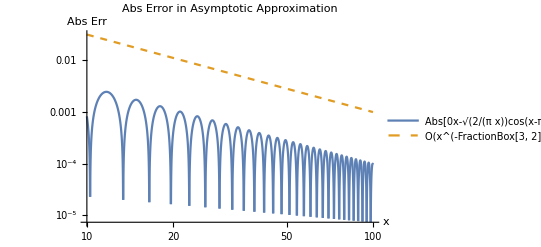

```mathematica
J0[x_]=√(2/(π x))Cos[x-π/4];
LogLogPlot[{Abs[J0[x]-BesselJ[0,x]],1/x^(3/2)},{x,10,100},
PlotLegends->{Abs[BesselJ[0,x]-"√(2/(π x))cos(x-π/4)"],"O(x^(-FractionBox[3, 2]))"},
PlotStyle->{Automatic,Dashed},
PlotLabel->"Abs Error in Asymptotic Approximation",
AxesLabel->{"x","Abs Err"}]
```

## 3)

### (a)

```mathematica
DSolveValue[{D[u[x,t], t]+D[u[x,t], x,x,x]==0,u[x,0]==u0[x]},u[x,t],{x,t}]
```

(ⅇ^(ⅈ x K[1]+ⅈ t K[1]^3) ∫_(-∞)^∞ ⅇ^(-ⅈ x K[1]) u0[x]ⅆxK[1]-∞∞)/(2 π)

```mathematica
DSolveValue[{D[u[k,t], t]-ⅈ k^3 u[k,t]==0,u[k,0]==u0[k]},u[k,t],{k,t}]
```

ⅇ^(ⅈ k^3 t) u0[k]

```mathematica
∫_(-∞)^∞ ((∫_(-∞)^∞ ⅇ^(-x^2)ⅇ^(-ⅈ k x)ⅆx) ⅇ^(ⅈ k x))ⅆk
```

2 ⅇ^(-x^2) π

```mathematica
Solve[3 k^2+x/t==0,k]
```

{{k→-(ⅈ √x)/(√3 √t)},{k→(ⅈ √x)/(√3 √t)}}

```mathematica
1/(2π)√(2/(t 6 √(-x/(3t))))(√π)/2//FullSimplify
```

(√(1/(t √(-x/t))))/(4 3^(1/4) √π)

### (b)

```mathematica
ϕ[k_]=ⅈ(k^3+k x/t);
z=kx+ⅈ ky;
u[kx_,ky_]=ky(ky^2-3 kx^2-x/t);
v[kx_,ky_]=kx(x/t+kx^2-3 ky^2);
Solve[∇_{kx,ky} u[kx,ky]==0,{kx,ky}]
Solve[∇_{kx,ky} v[kx,ky]==0,{kx,ky}]
```

{{kx→0,ky→-(√x)/(√3 √t)},{kx→0,ky→(√x)/(√3 √t)},{kx→-(ⅈ √x)/(√3 √t),ky→0},{kx→(ⅈ √x)/(√3 √t),ky→0}}

{{kx→0,ky→-(√x)/(√3 √t)},{kx→0,ky→(√x)/(√3 √t)},{kx→-(ⅈ √x)/(√3 √t),ky→0},{kx→(ⅈ √x)/(√3 √t),ky→0}}

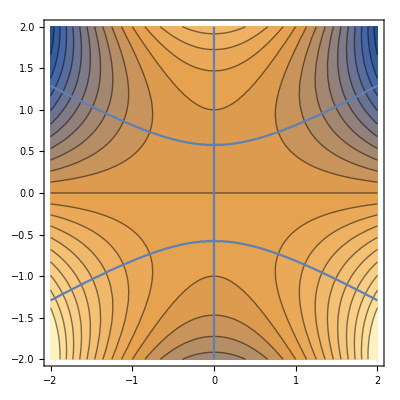

```mathematica
Show[ContourPlot[u[kx,ky]/.{x->1,t->1},{kx,-2,2},{ky,-2,2},Contours->20],
ContourPlot[(v[kx,ky]/.{x->1,t->1})==0,{kx,-2,2},{ky,-2,2},Contours->20]]
```

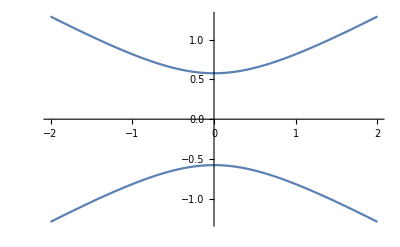

1+(ⅈ kx)/(3 √(kx^2/3+x/(3 t)))

```mathematica
Plot[{1,-1}√(1/3 kx^2+1/3),{kx,-2,2}]
D[(kx+ⅈ √(1/3 kx^2+x/(3t))), kx]
```

```mathematica
(D[u[kx,√(1/3 kx^2+x/(3t))], kx,kx])/.kx->0//FullSimplify
u[kx,√(1/3 kx^2+x/(3t))]/.kx->0//FullSimplify
```

-2 √3 √(x/t)

-(2 (x/t)^(3/2))/(3 √3)

```mathematica
NIntegrate[ⅈ ⅇ^((u[-10000000,ky]+ⅈ v[-10000000,ky])/.{x->1,t->1}),{ky,0,√(1/3 10000000^2+1/3)}]
```

2.07539×10^-15-2.60842×10^-15 ⅈ

### (c)

```mathematica
u0[x_]=ⅇ^(-x^2);
∫_(-∞)^∞ u0[x] ⅇ^(-ⅈ k x)ⅆx
√(π/(√(3x t)))(∫_(-∞)^∞ u0[y] ⅇ^(y √(x/(3t)))ⅆy) ⅇ^(-2/(3 √3)x √(x/t))
```

ⅇ^(-k^2/4) √π

(ⅇ^(x/(12 t)-(2 x √(x/t))/(3 √3)) π)/(3^(1/4) (t x)^(1/4))

```mathematica
ua[x_,t_]=π/(3x t)^(1/4)ⅇ^(x/(12t)-2/(3 √3)x √(x/t));
ut[x_,t_]:=Re[1/(2π)NIntegrate[ⅇ^(-k^2/4) √π ⅇ^(ⅈ(k^3 t+k x)),{k,-∞,∞}]];
Manipulate[Plot[{ua[x,t],ut[x,t]},{x,10,100},PlotRange->All],{t,10,2000}]
```

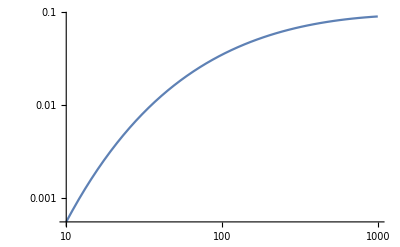

```mathematica
LogLogPlot[Abs[ut[15,t]-ua[15,t]],{t,10,1000}]
```